## Use Stirling Numbers to Define Chromatic Polynomials

```mathematica
chromaticPolynomial[n_,m_]:=Expand[FunctionExpand[Sum[StirlingS2[n,i]*FactorialPower[q,i]*(q-i)^m,{i,0,n}]]]
```

```mathematica
normalizedChromaticPolynomial[n_,m_]:=chromaticPolynomial[n,m]/.q->(n*m/(n+m))*q
```

```mathematica
nNChromaticPolynomial[n_,m_]:=normalizedChromaticPolynomial[n,m]/(Factorial[n]*Factorial[m])
```

```mathematica
chromaticRoots[n_,m_]:=NSolve[chromaticPolynomial[n,m]==0, q,WorkingPrecision->Log[n+2]]
```

```mathematica
chromaticPolynomial[6,6]/.q->2.1
```

-1127.39

```mathematica
chromaticPolynomial[2,2]
```

q (-3+6 q-4 q^2+q^3)

#### Magnitudes of Roots

```mathematica
chromaticRoots[50,50]
```

{{q→0},{q→1.},{q→2.},{q→3.},{q→4.},{q→5.},{q→6.},{q→7.},{q→8.},{q→9.},{q→10.},{q→11.},{q→12.},{q→13.},{q→14.},{q→15.},{q→16.},{q→17.},{q→18.},{q→19.},{q→20.},{q→21.},{q→22.},{q→23.},{q→23.82-0.34 ⅈ},{q→23.82+0.34 ⅈ},{q→24.18-1.1 ⅈ},{q→24.18+1.1 ⅈ},{q→24.54-1.9 ⅈ},{q→24.54+1.9 ⅈ},{q→24.9-2.79 ⅈ},{q→24.9+2.79 ⅈ},{q→25.24-3.67 ⅈ},{q→25.24+3.67 ⅈ},{q→25.58-4.56 ⅈ},{q→25.58+4.56 ⅈ},{q→25.92-5.49 ⅈ},{q→25.92+5.49 ⅈ},{q→26.24-6.45 ⅈ},{q→26.24+6.45 ⅈ},{q→26.57-7.43 ⅈ},{q→26.57+7.43 ⅈ},{q→26.88-8.45 ⅈ},{q→26.88+8.45 ⅈ},{q→27.19-9.5 ⅈ},{q→27.19+9.5 ⅈ},{q→27.49-10.6 ⅈ},{q→27.49+10.6 ⅈ},{q→27.78-11.7 ⅈ},{q→27.78+11.7 ⅈ},{q→28.07-12.9 ⅈ},{q→28.07+12.9 ⅈ},{q→28.35-14.1 ⅈ},{q→28.35+14.1 ⅈ},{q→28.63-15.3 ⅈ},{q→28.63+15.3 ⅈ},{q→28.9-16.6 ⅈ},{q→28.9+16.6 ⅈ},{q→29.2-17.9 ⅈ},{q→29.2+17.9 ⅈ},{q→29.4-19.3 ⅈ},{q→29.4+19.3 ⅈ},{q→29.7-20.7 ⅈ},{q→29.7+20.7 ⅈ},{q→29.9-22.2 ⅈ},{q→29.9+22.2 ⅈ},{q→30.2-23.7 ⅈ},{q→30.2+23.7 ⅈ},{q→30.4-25.3 ⅈ},{q→30.4+25.3 ⅈ},{q→30.6-27. ⅈ},{q→30.6+27. ⅈ},{q→30.9-28.7 ⅈ},{q→30.9+28.7 ⅈ},{q→31.1-30.5 ⅈ},{q→31.1+30.5 ⅈ},{q→31.3-32.4 ⅈ},{q→31.3+32.4 ⅈ},{q→31.5-34.4 ⅈ},{q→31.5+34.4 ⅈ},{q→31.8-36.5 ⅈ},{q→31.8+36.5 ⅈ},{q→32.-38.8 ⅈ},{q→32.+38.8 ⅈ},{q→32.2-41.1 ⅈ},{q→32.2+41.1 ⅈ},{q→32.4-43.6 ⅈ},{q→32.4+43.6 ⅈ},{q→32.6-46.3 ⅈ},{q→32.6+46.3 ⅈ},{q→32.8-49.2 ⅈ},{q→32.8+49.2 ⅈ},{q→33.1-52.4 ⅈ},{q→33.1+52.4 ⅈ},{q→33.3-56. ⅈ},{q→33.3+56. ⅈ},{q→33.5-60.17 ⅈ},{q→33.5+60.17 ⅈ},{q→33.8-65.4 ⅈ},{q→33.8+65.4 ⅈ}}

```mathematica
N[50*4/(Pi*E)]
```

23.4199

```mathematica
(*try for n=10*)
Abs[q/.chromaticRoots[10]]
```

{0.,1.,2.,3.,4.00037,4.86746,5.25673,5.25673,5.81053,5.81053,6.51764,6.51764,7.43619,7.43619,8.64425,8.64425,10.2702,10.2702,12.6146,12.6146}

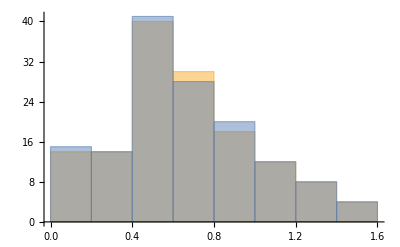

```mathematica
Histogram[Table[Abs[(q/n)/.chromaticRoots[n]],{n,70,71}]]
```

### Fitting Curves to Roots

```mathematica
filterRoots[roots_]:=Module[{newroots=List[]},
			For[i=1,i<=Length[roots], i++,If[Im[roots[[i]]]>0,AppendTo[newroots,roots[[i]]],0]];
Return[newroots]]
```

```mathematica
MapThread[List,{Re[Flatten[Table[filterRoots[(q/n - 4/(Pi*E))/.chromaticRoots[n]],{n,70,71}]]],Im[Flatten[Table[filterRoots[(q/n)/.chromaticRoots[n]],{n,70,71}]]]}]
```

{{0.00762594,0.00798533},{0.0128082,0.0193977},{0.0179333,0.0309921},{0.0229993,0.0428341},{0.0280047,0.0549304},{0.0329484,0.0672878},{0.0378294,0.0799135},{0.0426466,0.0928147},{0.0473991,0.105999},{0.0520864,0.119474},{0.0567078,0.133248},{0.0612631,0.147329},{0.0657521,0.161727},{0.070175,0.176451},{0.074532,0.19151},{0.0788235,0.206916},{0.0830502,0.22268},{0.0872125,0.238814},{0.0913114,0.255331},{0.0953477,0.272244},{0.0993224,0.289568},{0.103236,0.307318},{0.107091,0.325512},{0.110887,0.344165},{0.114626,0.363298},{0.118309,0.38293},{0.121938,0.403083},{0.125514,0.42378},{0.129039,0.445046},{0.132515,0.466908},{0.135943,0.489397},{0.139325,0.512544},{0.142664,0.536386},{0.145961,0.560961},{0.14922,0.586313},{0.152442,0.612491},{0.155631,0.63955},{0.15879,0.667552},{0.161922,0.696567},{0.165031,0.726678},{0.168121,0.75798},{0.171197,0.790585},{0.174265,0.824627},{0.177331,0.86027},{0.180404,0.897713},{0.183494,0.937213},{0.186614,0.979101},{0.189781,1.02382},{0.193021,1.07202},{0.196371,1.12463},{0.199894,1.18323},{0.203713,1.25084},{0.208155,1.3353},{0.00643493,0.00546171},{0.0114482,0.0164696},{0.0165168,0.0278368},{0.0215267,0.0394427},{0.0264781,0.0512938},{0.0313698,0.0633966},{0.036201,0.0757579},{0.0409704,0.0883846},{0.0456774,0.101284},{0.0503212,0.114463},{0.0549012,0.12793},{0.0594171,0.141692},{0.0638686,0.155758},{0.0682559,0.170137},{0.072579,0.184838},{0.0768384,0.199872},{0.0810345,0.215248},{0.0851679,0.230979},{0.0892392,0.247075},{0.0932493,0.26355},{0.097199,0.280417},{0.101089,0.297691},{0.104921,0.315386},{0.108696,0.33352},{0.112414,0.352108},{0.116077,0.37117},{0.119687,0.390726},{0.123244,0.410797},{0.126751,0.431406},{0.130209,0.452577},{0.133619,0.474338},{0.136983,0.496718},{0.140304,0.519749},{0.143583,0.543466},{0.146823,0.567907},{0.150026,0.593117},{0.153194,0.619143},{0.15633,0.64604},{0.159438,0.673868},{0.16252,0.702699},{0.165581,0.732613},{0.168624,0.763703},{0.171655,0.796082},{0.174679,0.829883},{0.177702,0.865265},{0.180733,0.902428},{0.183782,0.941626},{0.186861,0.983186},{0.189989,1.02755},{0.19319,1.07535},{0.1965,1.12751},{0.199983,1.18561},{0.203761,1.25264},{0.208156,1.33633}}

```mathematica
shiftedRoots=Table[filterRoots[(q/n-4/(Pi*E))/.chromaticRoots[n,n]],{n,40,45}]
```

{{0.012859+0.0150298 ⅈ,0.0219636+0.0354935 ⅈ,0.0308491+0.0566651 ⅈ,0.0395394+0.0786547 ⅈ,0.0480256+0.101499 ⅈ,0.0563015+0.125235 ⅈ,0.0643638+0.149903 ⅈ,0.0722122+0.1755485 ⅈ,0.0798488+0.2022214 ⅈ,0.0872775+0.2299782 ⅈ,0.0945035+0.2588828 ⅈ,0.101533+0.2890067 ⅈ,0.108372+0.3204303 ⅈ,0.115029+0.3532436 ⅈ,0.12151+0.3875477 ⅈ,0.127824+0.4234571 ⅈ,0.133981+0.4611024 ⅈ,0.139991+0.5006342 ⅈ,0.145863+0.542228 ⅈ,0.151611+0.5860915 ⅈ,0.157248+0.6324749 ⅈ,0.162791+0.6816853 ⅈ,0.168257+0.7341088 ⅈ,0.173669+0.7902456 ⅈ,0.179057+0.8507667 ⅈ,0.184459+0.9166163 ⅈ,0.189932+0.9892111 ⅈ,0.195568+1.070884 ⅈ,0.201544+1.166102 ⅈ,0.208328+1.286385 ⅈ},{0.010712+0.010267 ⅈ,0.0193882+0.0298616 ⅈ,0.0281058+0.0502895 ⅈ,0.0366387+0.0714853 ⅈ,0.0449803+0.0934823 ⅈ,0.0531241+0.116315 ⅈ,0.061066+0.14002 ⅈ,0.0688047+0.1646381 ⅈ,0.0763413+0.1902128 ⅈ,0.0836786+0.2167944 ⅈ,0.0908211+0.2444392 ⅈ,0.0977737+0.2732101 ⅈ,0.104542+0.3031775 ⅈ,0.111133+0.3344201 ⅈ,0.117554+0.3670257 ⅈ,0.12381+0.4010934 ⅈ,0.129912+0.436735 ⅈ,0.135867+0.474078 ⅈ,0.141684+0.5132698 ⅈ,0.147375+0.5544821 ⅈ,0.152951+0.5979183 ⅈ,0.158425+0.6438236 ⅈ,0.163812+0.692499 ⅈ,0.169132+0.7443237 ⅈ,0.174404+0.7997882 ⅈ,0.179659+0.8595514 ⅈ,0.184933+0.9245409 ⅈ,0.190282+0.9961481 ⅈ,0.195798+1.076665 ⅈ,0.201653+1.170483 ⅈ,0.208308+1.288924 ⅈ},{0.0075349+0.0058929 ⅈ,0.0169313+0.0245483 ⅈ,0.0254807+0.0442873 ⅈ,0.0338602+0.0647426 ⅈ,0.0420601+0.0859505 ⅈ,0.0500738+0.107943 ⅈ,0.0578968+0.1307538 ⅈ,0.065527+0.1544185 ⅈ,0.0729645+0.178977 ⅈ,0.0802112+0.2044737 ⅈ,0.0872705+0.2309583 ⅈ,0.0941469+0.2584863 ⅈ,0.100845+0.2871199 ⅈ,0.107371+0.316928 ⅈ,0.113731+0.3479876 ⅈ,0.119931+0.3803848 ⅈ,0.125979+0.4142163 ⅈ,0.131881+0.4495914 ⅈ,0.137646+0.4866349 ⅈ,0.143284+0.5254909 ⅈ,0.148805+0.5663277 ⅈ,0.154219+0.6093446 ⅈ,0.15954+0.6547821 ⅈ,0.164782+0.7029355 ⅈ,0.169963+0.7541768 ⅈ,0.175104+0.808988 ⅈ,0.180232+0.8680163 ⅈ,0.185385+0.932173 ⅈ,0.190618+1.002826 ⅈ,0.196018+1.082227 ⅈ,0.201758+1.174695 ⅈ,0.20829+1.291364 ⅈ},{0.0145799+0.0195579 ⅈ,0.0229665+0.0386266 ⅈ,0.0311967+0.0583898 ⅈ,0.039258+0.0788611 ⅈ,0.0471439+0.10007 ⅈ,0.0548497+0.1220479 ⅈ,0.0623726+0.1448267 ⅈ,0.0697118+0.1684425 ⅈ,0.0768685+0.1929347 ⅈ,0.0838453+0.2183475 ⅈ,0.0906457+0.2447302 ⅈ,0.0972742+0.2721376 ⅈ,0.103736+0.3006307 ⅈ,0.110036+0.3302773 ⅈ,0.11618+0.3611526 ⅈ,0.122174+0.3933409 ⅈ,0.128025+0.4269367 ⅈ,0.133741+0.462047 ⅈ,0.13933+0.498794 ⅈ,0.144799+0.5373188 ⅈ,0.15016+0.5777862 ⅈ,0.155422+0.6203918 ⅈ,0.160599+0.6653715 ⅈ,0.165704+0.7130152 ⅈ,0.170754+0.7636884 ⅈ,0.17577+0.8178645 ⅈ,0.180779+0.8761796 ⅈ,0.185818+0.9395295 ⅈ,0.190939+1.009259 ⅈ,0.19623+1.087584 ⅈ,0.20186+1.17875 ⅈ,0.208274+1.293711 ⅈ},{0.012273+0.0147774 ⅈ,0.0205573+0.0332791 ⅈ,0.0286417+0.0523942 ⅈ,0.0365675+0.0721765 ⅈ,0.044328+0.0926536 ⅈ,0.0519183+0.1138539 ⅈ,0.0593351+0.1358074 ⅈ,0.066577+0.1585462 ⅈ,0.0736444+0.1821059 ⅈ,0.0805392+0.2065257 ⅈ,0.0872641+0.2318496 ⅈ,0.0938231+0.2581264 ⅈ,0.10022+0.2854099 ⅈ,0.106461+0.3137601 ⅈ,0.112549+0.3432434 ⅈ,0.118491+0.3739335 ⅈ,0.124293+0.4059128 ⅈ,0.129961+0.4392739 ⅈ,0.135502+0.4741214 ⅈ,0.140924+0.510575 ⅈ,0.146236+0.5487731 ⅈ,0.151446+0.5888773 ⅈ,0.156565+0.6310795 ⅈ,0.161606+0.6756112 ⅈ,0.166581+0.7227574 ⅈ,0.171508+0.7728771 ⅈ,0.176406+0.8264355 ⅈ,0.181302+0.8840583 ⅈ,0.186231+0.9466263 ⅈ,0.191246+1.015462 ⅈ,0.196433+1.092746 ⅈ,0.201958+1.182656 ⅈ,0.20826+1.295972 ⅈ},{0.0103198+0.0102885 ⅈ,0.018245+0.0282207 ⅈ,0.026189+0.0467266 ⅈ,0.0339824+0.0658631 ⅈ,0.04162+0.0856549 ⅈ,0.0490966+0.1061285 ⅈ,0.0564087+0.1273113 ⅈ,0.0635544+0.1492325 ⅈ,0.0705332+0.1719243 ⅈ,0.0773465+0.1954218 ⅈ,0.0839965+0.2197642 ⅈ,0.0904862+0.2449951 ⅈ,0.0968194+0.2711624 ⅈ,0.103+0.2983193 ⅈ,0.109034+0.3265246 ⅈ,0.114924+0.3558433 ⅈ,0.120677+0.3863476 ⅈ,0.1262982+0.4181181 ⅈ,0.1317941+0.4512456 ⅈ,0.1371712+0.4858325 ⅈ,0.142437+0.5219962 ⅈ,0.1475997+0.5598722 ⅈ,0.1526683+0.5996193 ⅈ,0.1576528+0.6414259 ⅈ,0.1625647+0.6855194 ⅈ,0.1674175+0.7321798 ⅈ,0.172227+0.7817599 ⅈ,0.177013+0.8347176 ⅈ,0.181801+0.8916679 ⅈ,0.186627+0.9534776 ⅈ,0.191541+1.021448 ⅈ,0.196628+1.097725 ⅈ,0.202052+1.186421 ⅈ,0.208246+1.298151 ⅈ}}

```mathematica
test=FindFit[MapThread[List,{Re[Flatten[shiftedRoots]],Im[Flatten[shiftedRoots]]}],a*b^(x^2)+c,{a,b,c},x]
```

FindFit::nrlnum: The function value {0.02-0.0099017 ⅈ,-0.032364-0.028937 ⅈ,-0.10121-0.057229 ⅈ,«5»,-0.80345-0.39462 ⅈ,-0.96008-0.47457 ⅈ,«182»} is not a list of real numbers with dimensions {192} at {a,b,c} = {-19.045,-204.64,19.097}.

{a→-19.045,b→-204.64,c→19.097}

```mathematica
Log[(b/.test)]/Log[(/.)]
```

```mathematica
A/.test
```

4.42346

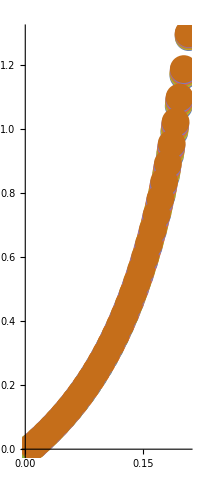

```mathematica
points=ComplexListPlot[shiftedRoots, PlotStyle->PointSize[0.05]]
```

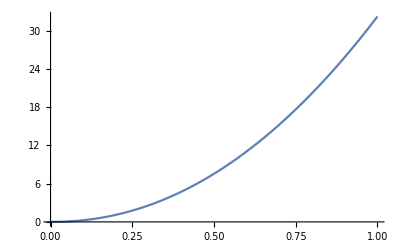

```mathematica
curve=Plot[(a/.test)*x^(c/.test),{x,0,1}]
```

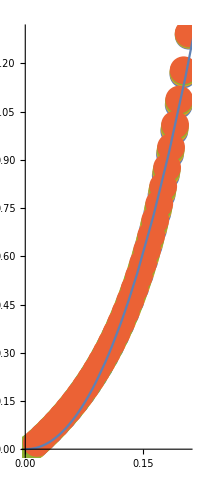

ComplexListPlot::lpn: {{},{{0.75,0.433013}},«8»,«10»} is not a list of numbers or pairs of numbers.

```mathematica
Show[points,curve]
```

### Real Plot of Polynomials

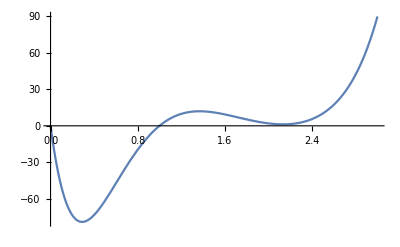

```mathematica
Plot[chromaticPolynomial[4,4],{q,0,3}]
```

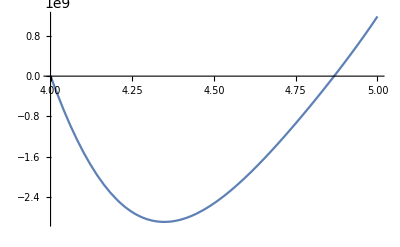

```mathematica
Plot[chromaticPolynomial[10,10],{q,4,5}]
```

```mathematica
Plot[chromaticPolynomial[20,20],{q,-0.1,11}]
```

-Graphics-

### Complex Plot of Polynomials

```mathematica
normalizedChromaticPolynomial[10,10]/.q->2
```

28729103428705770

```mathematica
N[Table[chromaticPolynomial[n,n]/.q->4*n/(Pi*E),{n,2,30}]]
```

{-0.0631867,1.10775,3.8604,-59.8625,-607.289,27803.4,829395.,-1.97524×10^7,-1.42626×10^9,7.26772×10^10,9.70337×10^12,-1.19651×10^14,-7.06082×10^16,2.02943×10^18,1.48221×10^21,4.88985×10^22,-2.95606×10^25,-1.24135×10^27,1.48731×10^30,2.08226×10^32,-6.12681×10^34,-1.33673×10^37,6.32076×10^39,2.40431×10^42,-3.98776×10^44,-2.9739×10^47,7.68653×10^49,8.07453×10^52,-1.70676×10^54}

```mathematica
N[Table[nNChromaticPolynomial[n,n]/.q->1,{n,60,70}]]
```

{7.17257×10^-15,4.58687×10^-15,2.93432×10^-15,1.8776×10^-15,1.20166×10^-15,7.6925×10^-16,4.92572×10^-16,3.15476×10^-16,2.02091×10^-16,1.29486×10^-16,8.29837×10^-17}

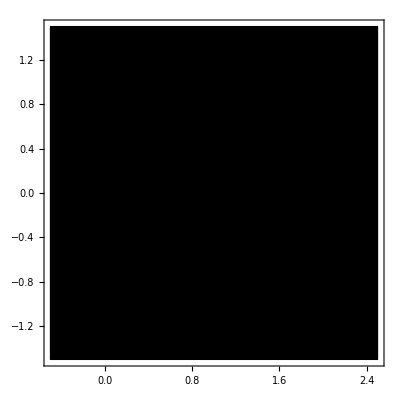

```mathematica
ComplexPlot[nNChromaticPolynomial[70,70],{q,-0.5-1.5I,2.5+1.5I}, ColorFunction->"QuantileAbs",PlotLegends->Automatic]
```

```mathematica
ComplexPlot3D[chromaticPolynomial[5],{q,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
fit=FindFit[MapThread[List,{Table[n,{n,2,20}],Table[chromaticPolynomial[n]/.q->5,{n,2,20}]}], a*b^x,{a,b,c},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→226.166,b→5.31235,c→1.}

```mathematica
pointsEval=ListPlot[MapThread[List,{Table[n,{n,2,20}],Table[chromaticPolynomial[n]/.q->5,{n,2,20}]}]]
```

-Graphics-

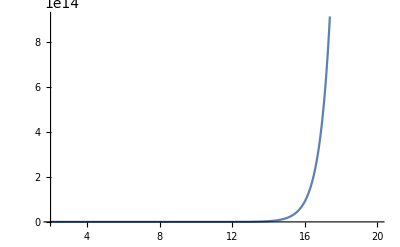

```mathematica
curveEval=Plot[(a/.fit)*(b/.fit)^x+(c/.fit),{x,2,20}]
```

```mathematica
Show[{pointsEval,curveEval}]
```

-Graphics-

```mathematica
rootsChromaticExample=Flatten[Table[(q/n)/.chromaticRoots[n],{n,2,35}]]
```

{0,0.5,0.7-0.4 ⅈ,0.7+0.4 ⅈ,0,0.33,0.62-0.2 ⅈ,0.62+0.2 ⅈ,0.71-0.65 ⅈ,0.71+0.65 ⅈ,0,0.25,0.54-0.04 ⅈ,0.54+0.04 ⅈ,0.64-0.34 ⅈ,0.64+0.34 ⅈ,0.7-0.77 ⅈ,0.7+0.77 ⅈ,0,0.2,0.401,0.537,0.59-0.2 ⅈ,0.59+0.2 ⅈ,0.647-0.466 ⅈ,0.647+0.466 ⅈ,0.694-0.858 ⅈ,0.694+0.858 ⅈ,0,0.167,0.333,0.488,0.556-0.115 ⅈ,0.556+0.115 ⅈ,0.609-0.309 ⅈ,0.609+0.309 ⅈ,0.652-0.561 ⅈ,0.652+0.561 ⅈ,0.69-0.919 ⅈ,0.69+0.919 ⅈ,0,0.143,0.286,0.428,0.5308-0.0648 ⅈ,0.5308+0.0648 ⅈ,0.5793-0.213 ⅈ,0.5793+0.213 ⅈ,0.62-0.398 ⅈ,0.62+0.398 ⅈ,0.655-0.635 ⅈ,0.655+0.635 ⅈ,0.687-0.967 ⅈ,0.687+0.967 ⅈ,0,0.125,0.25,0.375,0.5048-0.0293 ⅈ,0.5048+0.0293 ⅈ,0.556-0.149 ⅈ,0.556+0.149 ⅈ,0.5945-0.294 ⅈ,0.5945+0.294 ⅈ,0.6276-0.4705 ⅈ,0.6276+0.4705 ⅈ,0.6571-0.6948 ⅈ,0.6571+0.6948 ⅈ,0.685-1.004 ⅈ,0.685+1.004 ⅈ,0,0.1111,0.2222,0.3333,0.4457,0.5052,0.5369-0.103 ⅈ,0.5369+0.103 ⅈ,0.5736-0.2216 ⅈ,0.5736+0.2216 ⅈ,0.6052-0.3619 ⅈ,0.6052+0.3619 ⅈ,0.6332-0.5316 ⅈ,0.6332+0.5316 ⅈ,0.6588-0.7446 ⅈ,0.6588+0.7446 ⅈ,0.6835-1.035 ⅈ,0.6835+1.035 ⅈ,0,0.1,0.2,0.3,0.4,0.4867,0.5211-0.0691 ⅈ,0.5211+0.0691 ⅈ,0.556-0.1689 ⅈ,0.556+0.1689 ⅈ,0.5863-0.2847 ⅈ,0.5863+0.2847 ⅈ,0.6132-0.4206 ⅈ,0.6132+0.4206 ⅈ,0.6375-0.5838 ⅈ,0.6375+0.5838 ⅈ,0.6601-0.7868 ⅈ,0.6601+0.7868 ⅈ,0.6824-1.061 ⅈ,0.6824+1.061 ⅈ,0,0.09091,0.1818,0.2727,0.3636,0.4533,0.5088-0.0434 ⅈ,0.5088+0.0434 ⅈ,0.541-0.1288 ⅈ,0.541+0.1288 ⅈ,0.5701-0.227 ⅈ,0.5701+0.227 ⅈ,0.596-0.34 ⅈ,0.596+0.34 ⅈ,0.6194-0.4719 ⅈ,0.6194+0.4719 ⅈ,0.6409-0.629 ⅈ,0.6409+0.629 ⅈ,0.6612-0.823 ⅈ,0.6612+0.823 ⅈ,0.6815-1.083 ⅈ,0.6815+1.083 ⅈ,0,0.08333,0.1667,0.25,0.3333,0.4166,0.49559-0.0243 ⅈ,0.49559+0.0243 ⅈ,0.52806-0.09744 ⅈ,0.52806+0.09744 ⅈ,0.55593-0.1824 ⅈ,0.55593+0.1824 ⅈ,0.58095-0.2788 ⅈ,0.58095+0.2788 ⅈ,0.60361-0.3891 ⅈ,0.60361+0.3891 ⅈ,0.62435-0.5171 ⅈ,0.62435+0.5171 ⅈ,0.6436-0.6687 ⅈ,0.6436+0.6687 ⅈ,0.6621-0.8546 ⅈ,0.6621+0.8546 ⅈ,0.6808-1.1022 ⅈ,0.6808+1.1022 ⅈ,0,0.076923,0.15385,0.23077,0.30769,0.38461,0.46363,0.49265,0.51691-0.07229 ⅈ,0.51691+0.07229 ⅈ,0.54354-0.1469 ⅈ,0.54354+0.1469 ⅈ,0.56769-0.2307 ⅈ,0.56769+0.2307 ⅈ,0.58964-0.3254 ⅈ,0.58964+0.3254 ⅈ,0.60977-0.43306 ⅈ,0.60977+0.43306 ⅈ,0.6284-0.55736 ⅈ,0.6284+0.55736 ⅈ,0.64592-0.70374 ⅈ,0.64592+0.70374 ⅈ,0.66283-0.8824 ⅈ,0.66283+0.8824 ⅈ,0.6802-1.119 ⅈ,0.6802+1.119 ⅈ,0,0.071429,0.14286,0.21429,0.28571,0.35714,0.42864,0.48551,0.50705-0.05162 ⅈ,0.50705+0.05162 ⅈ,0.53261-0.118 ⅈ,0.53261+0.118 ⅈ,0.55589-0.192 ⅈ,0.55589+0.192 ⅈ,0.57718-0.27467 ⅈ,0.57718+0.27467 ⅈ,0.59674-0.36746 ⅈ,0.59674+0.36746 ⅈ,0.61485-0.47263 ⅈ,0.61485+0.47263 ⅈ,0.63178-0.59345 ⅈ,0.63178+0.59345 ⅈ,0.64784-0.73507 ⅈ,0.64784+0.73507 ⅈ,0.6635-0.9071 ⅈ,0.6635+0.9071 ⅈ,0.67976-1.1338 ⅈ,0.67976+1.1338 ⅈ,0,0.066667,0.13333,0.2,0.26667,0.33333,0.4,0.46478,0.49899-0.03431 ⅈ,0.49899+0.03431 ⅈ,0.52292-0.09413 ⅈ,0.52292+0.09413 ⅈ,0.54535-0.16024 ⅈ,0.54535+0.16024 ⅈ,0.56598-0.23345 ⅈ,0.56598+0.23345 ⅈ,0.58501-0.31479 ⅈ,0.58501+0.31479 ⅈ,0.60266-0.40578 ⅈ,0.60266+0.40578 ⅈ,0.61913-0.50851 ⅈ,0.61913+0.50851 ⅈ,0.63465-0.62605 ⅈ,0.63465+0.62605 ⅈ,0.64949-0.76325 ⅈ,0.64949+0.76325 ⅈ,0.66408-0.92923 ⅈ,0.66408+0.92923 ⅈ,0.67936-1.1471 ⅈ,0.67936+1.1471 ⅈ,0,0.0625,0.125,0.1875,0.25,0.3125,0.375,0.43741,0.49097-0.02111 ⅈ,0.49097+0.02111 ⅈ,0.51429-0.07407 ⅈ,0.51429+0.07407 ⅈ,0.53587-0.1337 ⅈ,0.53587+0.1337 ⅈ,0.55586-0.19929 ⅈ,0.55586+0.19929 ⅈ,0.57438-0.27159 ⅈ,0.57438+0.27159 ⅈ,0.59159-0.35162 ⅈ,0.59159+0.35162 ⅈ,0.60767-0.44084 ⅈ,0.60767+0.44084 ⅈ,0.62278-0.54122 ⅈ,0.62278+0.54122 ⅈ,0.63711-0.65566 ⅈ,0.63711+0.65566 ⅈ,0.65092-0.78875 ⅈ,0.65092+0.78875 ⅈ,0.66459-0.94919 ⅈ,0.66459+0.94919 ⅈ,0.67902-1.159 ⅈ,0.67902+1.159 ⅈ,0,0.058824,0.11765,0.17647,0.23529,0.29412,0.35294,0.41176,0.47643,0.48238,0.50659-0.05703 ⅈ,0.50659+0.05703 ⅈ,0.52732-0.11122 ⅈ,0.52732+0.11122 ⅈ,0.54668-0.17055 ⅈ,0.54668+0.17055 ⅈ,0.56469-0.23551 ⅈ,0.56469+0.23551 ⅈ,0.58149-0.30684 ⅈ,0.58149+0.30684 ⅈ,0.5972-0.38557 ⅈ,0.5972+0.38557 ⅈ,0.61196-0.47306 ⅈ,0.61196+0.47306 ⅈ,0.62592-0.5712 ⅈ,0.62592+0.5712 ⅈ,0.63925-0.6827 ⅈ,0.63925+0.6827 ⅈ,0.65217-0.81197 ⅈ,0.65217+0.81197 ⅈ,0.66505-0.9673 ⅈ,0.66505+0.9673 ⅈ,0.67874-1.1698 ⅈ,0.67874+1.1698 ⅈ,0,0.055556,0.11111,0.16667,0.22222,0.27778,0.33333,0.38889,0.44457,0.48409,0.49959-0.04237 ⅈ,0.49959+0.04237 ⅈ,0.51958-0.091969 ⅈ,0.51958+0.091969 ⅈ,0.53831-0.14605 ⅈ,0.53831+0.14605 ⅈ,0.55583-0.20495 ⅈ,0.55583+0.20495 ⅈ,0.57222-0.2692 ⅈ,0.57222+0.2692 ⅈ,0.58758-0.33955 ⅈ,0.58758+0.33955 ⅈ,0.60204-0.41699 ⅈ,0.60204+0.41699 ⅈ,0.61569-0.5028 ⅈ,0.61569+0.5028 ⅈ,0.62867-0.59878 ⅈ,0.62867+0.59878 ⅈ,0.64114-0.70752 ⅈ,0.64114+0.70752 ⅈ,0.65329-0.83322 ⅈ,0.65329+0.83322 ⅈ,0.66547-0.98383 ⅈ,0.66547+0.98383 ⅈ,0.67849-1.1796 ⅈ,0.67849+1.1796 ⅈ,0,0.052632,0.10526,0.15789,0.21053,0.26316,0.31579,0.36842,0.42106,0.47084,0.493501-0.02936 ⅈ,0.493501+0.02936 ⅈ,0.512561-0.075308 ⅈ,0.512561+0.075308 ⅈ,0.530673-0.12494 ⅈ,0.530673+0.12494 ⅈ,0.5477-0.17875 ⅈ,0.5477+0.17875 ⅈ,0.563686-0.23713 ⅈ,0.563686+0.23713 ⅈ,0.57871-0.30064 ⅈ,0.57871+0.30064 ⅈ,0.59287-0.37 ⅈ,0.59287+0.37 ⅈ,0.60625-0.44616 ⅈ,0.60625+0.44616 ⅈ,0.61896-0.53035 ⅈ,0.61896+0.53035 ⅈ,0.63109-0.62427 ⅈ,0.63109+0.62427 ⅈ,0.64281-0.73039 ⅈ,0.64281+0.73039 ⅈ,0.65428-0.85276 ⅈ,0.65428+0.85276 ⅈ,0.66584-0.99899 ⅈ,0.66584+0.99899 ⅈ,0.67827-1.1886 ⅈ,0.67827+1.1886 ⅈ,0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.44984,0.488041-0.01898 ⅈ,0.488041+0.01898 ⅈ,0.506164-0.060753 ⅈ,0.506164+0.060753 ⅈ,0.523673-0.10656 ⅈ,0.523673+0.10656 ⅈ,0.540216-0.15604 ⅈ,0.540216+0.15604 ⅈ,0.555807-0.20948 ⅈ,0.555807+0.20948 ⅈ,0.570502-0.26731 ⅈ,0.570502+0.26731 ⅈ,0.584374-0.33006 ⅈ,0.584374+0.33006 ⅈ,0.597501-0.39844 ⅈ,0.597501+0.39844 ⅈ,0.609962-0.47334 ⅈ,0.609962+0.47334 ⅈ,0.621844-0.55596 ⅈ,0.621844+0.55596 ⅈ,0.63325-0.6479 ⅈ,0.63325+0.6479 ⅈ,0.6443-0.751548 ⅈ,0.6443+0.751548 ⅈ,0.65518-0.870786 ⅈ,0.65518+0.870786 ⅈ,0.66619-1.01295 ⅈ,0.66619+1.01295 ⅈ,0.67808-1.19682 ⅈ,0.67808+1.19682 ⅈ,0,0.047619,0.0952381,0.142857,0.190476,0.238095,0.285714,0.333333,0.380952,0.428565,0.479963-0.008019 ⅈ,0.479963+0.008019 ⅈ,0.500344-0.047935 ⅈ,0.500344+0.047935 ⅈ,0.517245-0.090443 ⅈ,0.517245+0.090443 ⅈ,0.533311-0.13619 ⅈ,0.533311+0.13619 ⅈ,0.548511-0.18542 ⅈ,0.548511+0.18542 ⅈ,0.562879-0.23844 ⅈ,0.562879+0.23844 ⅈ,0.576473-0.29567 ⅈ,0.576473+0.29567 ⅈ,0.589355-0.35765 ⅈ,0.589355+0.35765 ⅈ,0.601592-0.425055 ⅈ,0.601592+0.425055 ⅈ,0.613253-0.49874 ⅈ,0.613253+0.49874 ⅈ,0.624416-0.579832 ⅈ,0.624416+0.579832 ⅈ,0.635173-0.669885 ⅈ,0.635173+0.669885 ⅈ,0.645641-0.771193 ⅈ,0.645641+0.771193 ⅈ,0.655988-0.88749 ⅈ,0.655988+0.88749 ⅈ,0.66651-1.02586 ⅈ,0.66651+1.02586 ⅈ,0.67792-1.20444 ⅈ,0.67792+1.20444 ⅈ,0,0.0454545,0.0909091,0.136364,0.181818,0.227273,0.272727,0.318182,0.363636,0.409091,0.454785,0.482566,0.494972-0.036607 ⅈ,0.494972+0.036607 ⅈ,0.51133-0.07619 ⅈ,0.51133+0.07619 ⅈ,0.526925-0.1187 ⅈ,0.526925+0.1187 ⅈ,0.54174-0.16429 ⅈ,0.54174+0.16429 ⅈ,0.555785-0.2132 ⅈ,0.555785+0.2132 ⅈ,0.569105-0.26576 ⅈ,0.569105+0.26576 ⅈ,0.581749-0.322388 ⅈ,0.581749+0.322388 ⅈ,0.593772-0.383599 ⅈ,0.593772+0.383599 ⅈ,0.605234-0.450039 ⅈ,0.605234+0.450039 ⅈ,0.616194-0.522531 ⅈ,0.616194+0.522531 ⅈ,0.626724-0.602154 ⅈ,0.626724+0.602154 ⅈ,0.636908-0.690403 ⅈ,0.636908+0.690403 ⅈ,0.646856-0.78949 ⅈ,0.646856+0.78949 ⅈ,0.656727-0.90302 ⅈ,0.656727+0.90302 ⅈ,0.666801-1.03784 ⅈ,0.666801+1.03784 ⅈ,0.677777-1.2115 ⅈ,0.677777+1.2115 ⅈ,0,0.0434783,0.0869565,0.130435,0.173913,0.217391,0.26087,0.304348,0.347826,0.391304,0.434791,0.474171,0.490049-0.02628 ⅈ,0.490049+0.02628 ⅈ,0.505875-0.063503 ⅈ,0.505875+0.063503 ⅈ,0.521009-0.10317 ⅈ,0.521009+0.10317 ⅈ,0.535442-0.14559 ⅈ,0.535442+0.14559 ⅈ,0.549169-0.19095 ⅈ,0.549169+0.19095 ⅈ,0.562217-0.239513 ⅈ,0.562217+0.239513 ⅈ,0.574627-0.291596 ⅈ,0.574627+0.291596 ⅈ,0.586444-0.347609 ⅈ,0.586444+0.347609 ⅈ,0.597717-0.408051 ⅈ,0.597717+0.408051 ⅈ,0.608496-0.473543 ⅈ,0.608496+0.473543 ⅈ,0.618837-0.544873 ⅈ,0.618837+0.544873 ⅈ,0.628806-0.623079 ⅈ,0.628806+0.623079 ⅈ,0.63848-0.709603 ⅈ,0.63848+0.709603 ⅈ,0.647962-0.806582 ⅈ,0.647962+0.806582 ⅈ,0.657404-0.917502 ⅈ,0.657404+0.917502 ⅈ,0.667074-1.049 ⅈ,0.667074+1.049 ⅈ,0.67765-1.21805 ⅈ,0.67765+1.21805 ⅈ,0,0.0416667,0.0833333,0.125,0.166667,0.208333,0.25,0.291667,0.333333,0.375,0.416667,0.458029,0.485924-0.017508 ⅈ,0.485924+0.017508 ⅈ,0.500829-0.05214 ⅈ,0.500829+0.05214 ⅈ,0.515516-0.089309 ⅈ,0.515516+0.089309 ⅈ,0.529574-0.12894 ⅈ,0.529574+0.12894 ⅈ,0.542987-0.17121 ⅈ,0.542987+0.17121 ⅈ,0.555767-0.216298 ⅈ,0.555767+0.216298 ⅈ,0.567945-0.264477 ⅈ,0.567945+0.264477 ⅈ,0.57956-0.316068 ⅈ,0.57956+0.316068 ⅈ,0.590652-0.371462 ⅈ,0.590652+0.371462 ⅈ,0.601262-0.431142 ⅈ,0.601262+0.431142 ⅈ,0.611437-0.495702 ⅈ,0.611437+0.495702 ⅈ,0.621228-0.565902 ⅈ,0.621228+0.565902 ⅈ,0.630695-0.642742 ⅈ,0.630695+0.642742 ⅈ,0.639911-0.727617 ⅈ,0.639911+0.727617 ⅈ,0.648973-0.822591 ⅈ,0.648973+0.822591 ⅈ,0.658026-0.931046 ⅈ,0.658026+0.931046 ⅈ,0.667329-1.05941 ⅈ,0.667329+1.05941 ⅈ,0.677537-1.22417 ⅈ,0.677537+1.22417 ⅈ,0,0.04,0.08,0.12,0.16,0.2,0.24,0.28,0.32,0.36,0.4,0.439988,0.480125-0.00961 ⅈ,0.480125+0.00961 ⅈ,0.496164-0.041898 ⅈ,0.496164+0.041898 ⅈ,0.510409-0.076855 ⅈ,0.510409+0.076855 ⅈ,0.524098-0.11403 ⅈ,0.524098+0.11403 ⅈ,0.537199-0.153563 ⅈ,0.537199+0.153563 ⅈ,0.549714-0.195623 ⅈ,0.549714+0.195623 ⅈ,0.561664-0.240415 ⅈ,0.561664+0.240415 ⅈ,0.57308-0.288198 ⅈ,0.57308+0.288198 ⅈ,0.583994-0.339287 ⅈ,0.583994+0.339287 ⅈ,0.594443-0.394062 ⅈ,0.594443+0.394062 ⅈ,0.604466-0.452987 ⅈ,0.604466+0.452987 ⅈ,0.614103-0.516635 ⅈ,0.614103+0.516635 ⅈ,0.623402-0.585737 ⅈ,0.623402+0.585737 ⅈ,0.632418-0.661262 ⅈ,0.632418+0.661262 ⅈ,0.641221-0.744556 ⅈ,0.641221+0.744556 ⅈ,0.649903-0.837625 ⅈ,0.649903+0.837625 ⅈ,0.658601-0.943745 ⅈ,0.658601+0.943745 ⅈ,0.667566-1.06916 ⅈ,0.667566+1.06916 ⅈ,0.677437-1.22989 ⅈ,0.677437+1.22989 ⅈ,0,0.0384615,0.0769231,0.115385,0.153846,0.192308,0.230769,0.269231,0.307692,0.346154,0.384615,0.423076,0.462023,0.480901,0.491827-0.032665 ⅈ,0.491827+0.032665 ⅈ,0.505651-0.06561 ⅈ,0.505651+0.06561 ⅈ,0.518979-0.10059 ⅈ,0.518979+0.10059 ⅈ,0.531773-0.137711 ⅈ,0.531773+0.137711 ⅈ,0.544026-0.177098 ⅈ,0.544026+0.177098 ⅈ,0.55575-0.218923 ⅈ,0.55575+0.218923 ⅈ,0.566968-0.263395 ⅈ,0.566968+0.263395 ⅈ,0.577708-0.31077 ⅈ,0.577708+0.31077 ⅈ,0.588001-0.361352 ⅈ,0.588001+0.361352 ⅈ,0.597879-0.41551 ⅈ,0.597879+0.41551 ⅈ,0.607376-0.473691 ⅈ,0.607376+0.473691 ⅈ,0.61653-0.536446 ⅈ,0.61653+0.536446 ⅈ,0.625387-0.604483 ⅈ,0.625387+0.604483 ⅈ,0.633997-0.67874 ⅈ,0.633997+0.67874 ⅈ,0.642425-0.760522 ⅈ,0.642425+0.760522 ⅈ,0.65076-0.851774 ⅈ,0.65076+0.851774 ⅈ,0.659134-0.955682 ⅈ,0.659134+0.955682 ⅈ,0.667789-1.07832 ⅈ,0.667789+1.07832 ⅈ,0.677347-1.23525 ⅈ,0.677347+1.23525 ⅈ,0,0.037037,0.0740741,0.111111,0.148148,0.185185,0.222222,0.259259,0.296296,0.333333,0.37037,0.407407,0.444462,0.475949,0.487716-0.024157 ⅈ,0.487716+0.024157 ⅈ,0.501211-0.055407 ⅈ,0.501211+0.055407 ⅈ,0.514186-0.088432 ⅈ,0.514186+0.088432 ⅈ,0.526679-0.123394 ⅈ,0.526679+0.123394 ⅈ,0.538673-0.160408 ⅈ,0.538673+0.160408 ⅈ,0.550173-0.199614 ⅈ,0.550173+0.199614 ⅈ,0.561196-0.241182 ⅈ,0.561196+0.241182 ⅈ,0.571764-0.28532 ⅈ,0.571764+0.28532 ⅈ,0.581903-0.332278 ⅈ,0.581903+0.332278 ⅈ,0.591641-0.382352 ⅈ,0.591641+0.382352 ⅈ,0.601006-0.435897 ⅈ,0.601006+0.435897 ⅈ,0.610031-0.493345 ⅈ,0.610031+0.493345 ⅈ,0.618751-0.555228 ⅈ,0.618751+0.555228 ⅈ,0.627207-0.622233 ⅈ,0.627207+0.622233 ⅈ,0.635448-0.695268 ⅈ,0.635448+0.695268 ⅈ,0.643536-0.7756 ⅈ,0.643536+0.7756 ⅈ,0.651554-0.865121 ⅈ,0.651554+0.865121 ⅈ,0.659629-0.966928 ⅈ,0.659629+0.966928 ⅈ,0.667999-1.08693 ⅈ,0.667999+1.08693 ⅈ,0.677268-1.24029 ⅈ,0.677268+1.24029 ⅈ,0,0.0357143,0.0714286,0.107143,0.142857,0.178571,0.214286,0.25,0.285714,0.321429,0.357143,0.392857,0.428572,0.463726,0.484294-0.016493 ⅈ,0.484294+0.016493 ⅈ,0.497059-0.04611 ⅈ,0.497059+0.04611 ⅈ,0.509694-0.077373 ⅈ,0.509694+0.077373 ⅈ,0.521889-0.110403 ⅈ,0.521889+0.110403 ⅈ,0.533628-0.145298 ⅈ,0.533628+0.145298 ⅈ,0.544907-0.182175 ⅈ,0.544907+0.182175 ⅈ,0.555736-0.221175 ⅈ,0.555736+0.221175 ⅈ,0.566134-0.26247 ⅈ,0.566134+0.26247 ⅈ,0.576121-0.306264 ⅈ,0.576121+0.306264 ⅈ,0.585722-0.3528 ⅈ,0.585722+0.3528 ⅈ,0.594961-0.402366 ⅈ,0.594961+0.402366 ⅈ,0.603866-0.455304 ⅈ,0.603866+0.455304 ⅈ,0.612465-0.512031 ⅈ,0.612465+0.512031 ⅈ,0.620791-0.573065 ⅈ,0.620791+0.573065 ⅈ,0.628884-0.639069 ⅈ,0.628884+0.639069 ⅈ,0.636789-0.710925 ⅈ,0.636789+0.710925 ⅈ,0.644564-0.789867 ⅈ,0.644564+0.789867 ⅈ,0.652291-0.877735 ⅈ,0.652291+0.877735 ⅈ,0.660092-0.977545 ⅈ,0.660092+0.977545 ⅈ,0.668197-1.09505 ⅈ,0.668197+1.09505 ⅈ,0.677196-1.24504 ⅈ,0.677196+1.24504 ⅈ,0,0.0344828,0.0689655,0.103448,0.137931,0.172414,0.206897,0.241379,0.275862,0.310345,0.344828,0.37931,0.413793,0.448251,0.480047-0.010125 ⅈ,0.480047+0.010125 ⅈ,0.493173-0.037595 ⅈ,0.493173+0.037595 ⅈ,0.505475-0.067276 ⅈ,0.505475+0.067276 ⅈ,0.517381-0.0985644 ⅈ,0.517381+0.0985644 ⅈ,0.528868-0.131556 ⅈ,0.528868+0.131556 ⅈ,0.539927-0.16635 ⅈ,0.539927+0.16635 ⅈ,0.550565-0.203065 ⅈ,0.550565+0.203065 ⅈ,0.560794-0.241842 ⅈ,0.560794+0.241842 ⅈ,0.570631-0.282852 ⅈ,0.570631+0.282852 ⅈ,0.580098-0.326295 ⅈ,0.580098+0.326295 ⅈ,0.589214-0.372407 ⅈ,0.589214+0.372407 ⅈ,0.598004-0.421466 ⅈ,0.598004+0.421466 ⅈ,0.606491-0.473804 ⅈ,0.606491+0.473804 ⅈ,0.614704-0.529824 ⅈ,0.614704+0.529824 ⅈ,0.622672-0.590029 ⅈ,0.622672+0.590029 ⅈ,0.630433-0.655063 ⅈ,0.630433+0.655063 ⅈ,0.638031-0.725784 ⅈ,0.638031+0.725784 ⅈ,0.64552-0.803392 ⅈ,0.64552+0.803392 ⅈ,0.652978-0.889679 ⅈ,0.652978+0.889679 ⅈ,0.660525-0.987587 ⅈ,0.660525+0.987587 ⅈ,0.668384-1.10273 ⅈ,0.668384+1.10273 ⅈ,0.677132-1.24952 ⅈ,0.677132+1.24952 ⅈ,0,0.0333333,0.0666667,0.1,0.133333,0.166667,0.2,0.233333,0.266667,0.3,0.333333,0.366667,0.4,0.433332,0.467749,0.478884,0.48954-0.029798 ⅈ,0.48954+0.029798 ⅈ,0.501509-0.0580206 ⅈ,0.501509+0.0580206 ⅈ,0.513132-0.0877338 ⅈ,0.513132+0.0877338 ⅈ,0.524371-0.119007 ⅈ,0.524371+0.119007 ⅈ,0.535214-0.151928 ⅈ,0.535214+0.151928 ⅈ,0.545662-0.186595 ⅈ,0.545662+0.186595 ⅈ,0.555723-0.223129 ⅈ,0.555723+0.223129 ⅈ,0.565412-0.26167 ⅈ,0.565412+0.26167 ⅈ,0.574746-0.302386 ⅈ,0.574746+0.302386 ⅈ,0.583742-0.345473 ⅈ,0.583742+0.345473 ⅈ,0.59242-0.39116 ⅈ,0.59242+0.39116 ⅈ,0.600802-0.439716 ⅈ,0.600802+0.439716 ⅈ,0.60891-0.491462 ⅈ,0.60891+0.491462 ⅈ,0.616771-0.54679 ⅈ,0.616771+0.54679 ⅈ,0.624413-0.606188 ⅈ,0.624413+0.606188 ⅈ,0.63187-0.670281 ⅈ,0.63187+0.670281 ⅈ,0.639185-0.739907 ⅈ,0.639185+0.739907 ⅈ,0.64641-0.816234 ⅈ,0.64641+0.816234 ⅈ,0.65362-0.901009 ⅈ,0.65362+0.901009 ⅈ,0.660932-0.997103 ⅈ,0.660932+0.997103 ⅈ,0.668562-1.10999 ⅈ,0.668562+1.10999 ⅈ,0.677074-1.25376 ⅈ,0.677074+1.25376 ⅈ,0,0.0322581,0.0645161,0.0967742,0.129032,0.16129,0.193548,0.225806,0.258065,0.290323,0.322581,0.354839,0.387097,0.419355,0.451649,0.476788,0.4860445-0.022584 ⅈ,0.4860445+0.022584 ⅈ,0.4977759-0.0495066 ⅈ,0.4977759+0.0495066 ⅈ,0.5091222-0.0777892 ⅈ,0.5091222+0.0777892 ⅈ,0.5201175-0.107506 ⅈ,0.5201175+0.107506 ⅈ,0.5307472-0.138733 ⅈ,0.5307472+0.138733 ⅈ,0.541007-0.171557 ⅈ,0.541007+0.171557 ⅈ,0.550903-0.206078 ⅈ,0.550903+0.206078 ⅈ,0.560445-0.242416 ⅈ,0.560445+0.242416 ⅈ,0.569646-0.280711 ⅈ,0.569646+0.280711 ⅈ,0.578523-0.321127 ⅈ,0.578523+0.321127 ⅈ,0.587093-0.363855 ⅈ,0.587093+0.363855 ⅈ,0.595374-0.409117 ⅈ,0.595374+0.409117 ⅈ,0.603384-0.457174 ⅈ,0.603384+0.457174 ⅈ,0.611147-0.508337 ⅈ,0.611147+0.508337 ⅈ,0.618686-0.562988 ⅈ,0.618686+0.562988 ⅈ,0.626028-0.621599 ⅈ,0.626028+0.621599 ⅈ,0.633206-0.684782 ⅈ,0.633206+0.684782 ⅈ,0.64026-0.753351 ⅈ,0.64026+0.753351 ⅈ,0.647242-0.828446 ⅈ,0.647242+0.828446 ⅈ,0.654222-0.911774 ⅈ,0.654222+0.911774 ⅈ,0.661314-1.00614 ⅈ,0.661314+1.00614 ⅈ,0.66873-1.11688 ⅈ,0.66873+1.11688 ⅈ,0.677021-1.25778 ⅈ,0.677021+1.25778 ⅈ,0,0.03125,0.0625,0.09375,0.125,0.15625,0.1875,0.21875,0.25,0.28125,0.3125,0.34375,0.375,0.40625,0.437501,0.467758,0.4830139-0.015809 ⅈ,0.4830139+0.015809 ⅈ,0.4942551-0.0416503 ⅈ,0.4942551+0.0416503 ⅈ,0.5053341-0.068627 ⅈ,0.5053341+0.068627 ⅈ,0.5160911-0.0969265 ⅈ,0.5160911+0.0969265 ⅈ,0.5265105-0.126617 ⅈ,0.5265105+0.126617 ⅈ,0.536585-0.157772 ⅈ,0.536585+0.157772 ⅈ,0.5463163-0.190479 ⅈ,0.5463163+0.190479 ⅈ,0.5557117-0.224839 ⅈ,0.5557117+0.224839 ⅈ,0.5647824-0.260971 ⅈ,0.5647824+0.260971 ⅈ,0.5735419-0.299013 ⅈ,0.5735419+0.299013 ⅈ,0.5820046-0.339125 ⅈ,0.5820046+0.339125 ⅈ,0.5901863-0.381493 ⅈ,0.5901863+0.381493 ⅈ,0.598104-0.426331 ⅈ,0.598104+0.426331 ⅈ,0.605775-0.473894 ⅈ,0.605775+0.473894 ⅈ,0.613222-0.524484 ⅈ,0.613222+0.524484 ⅈ,0.620465-0.578472 ⅈ,0.620465+0.578472 ⅈ,0.627532-0.636318 ⅈ,0.627532+0.636318 ⅈ,0.634453-0.698619 ⅈ,0.634453+0.698619 ⅈ,0.641266-0.766167 ⅈ,0.641266+0.766167 ⅈ,0.648021-0.840078 ⅈ,0.648021+0.840078 ⅈ,0.654787-0.922018 ⅈ,0.654787+0.922018 ⅈ,0.661674-1.014724 ⅈ,0.661674+1.014724 ⅈ,0.66889-1.123428 ⅈ,0.66889+1.123428 ⅈ,0.676974-1.261594 ⅈ,0.676974+1.261594 ⅈ,0,0.030303,0.0606061,0.0909091,0.121212,0.151515,0.181818,0.212121,0.242424,0.272727,0.30303,0.333333,0.363636,0.393939,0.424242,0.454495,0.4798165-0.010266 ⅈ,0.4798165+0.010266 ⅈ,0.4909288-0.034372 ⅈ,0.4909288+0.034372 ⅈ,0.501751-0.0601593 ⅈ,0.501751+0.0601593 ⅈ,0.5122753-0.0871646 ⅈ,0.5122753+0.0871646 ⅈ,0.5224877-0.115454 ⅈ,0.5224877+0.115454 ⅈ,0.532379-0.145093 ⅈ,0.532379+0.145093 ⅈ,0.5419475-0.176157 ⅈ,0.5419475+0.176157 ⅈ,0.5511979-0.208732 ⅈ,0.5511979+0.208732 ⅈ,0.5601388-0.242919 ⅈ,0.5601388+0.242919 ⅈ,0.5687815-0.278837 ⅈ,0.5687815+0.278837 ⅈ,0.5771383-0.31662 ⅈ,0.5771383+0.31662 ⅈ,0.585223-0.356425 ⅈ,0.585223+0.356425 ⅈ,0.5930501-0.398431 ⅈ,0.5930501+0.398431 ⅈ,0.6006354-0.442849 ⅈ,0.6006354+0.442849 ⅈ,0.607996-0.489924 ⅈ,0.607996+0.489924 ⅈ,0.6151513-0.539951 ⅈ,0.6151513+0.539951 ⅈ,0.6221227-0.593291 ⅈ,0.6221227+0.593291 ⅈ,0.628935-0.6503927 ⅈ,0.628935+0.6503927 ⅈ,0.635618-0.7118376 ⅈ,0.635618+0.7118376 ⅈ,0.642208-0.7784013 ⅈ,0.642208+0.7784013 ⅈ,0.648752-0.8511724 ⅈ,0.648752+0.8511724 ⅈ,0.655319-0.93178 ⅈ,0.655319+0.93178 ⅈ,0.662015-1.022902 ⅈ,0.662015+1.022902 ⅈ,0.669043-1.129656 ⅈ,0.669043+1.129656 ⅈ,0.676932-1.265219 ⅈ,0.676932+1.265219 ⅈ,0,0.02941176,0.05882353,0.08823529,0.1176471,0.1470588,0.1764706,0.2058824,0.2352941,0.2647059,0.2941176,0.3235294,0.3529412,0.3823529,0.4117647,0.4411745,0.4745663-0.001645 ⅈ,0.4745663+0.001645 ⅈ,0.4877998-0.027623 ⅈ,0.4877998+0.027623 ⅈ,0.4983578-0.0523104 ⅈ,0.4983578+0.0523104 ⅈ,0.5086553-0.0781298 ⅈ,0.5086553+0.0781298 ⅈ,0.5186646-0.105138 ⅈ,0.5186646+0.105138 ⅈ,0.5283751-0.133393 ⅈ,0.5283751+0.133393 ⅈ,0.5377826-0.162962 ⅈ,0.5377826+0.162962 ⅈ,0.5468893-0.193919 ⅈ,0.5468893+0.193919 ⅈ,0.5557014-0.22635 ⅈ,0.5557014+0.22635 ⅈ,0.564228-0.260356 ⅈ,0.564228+0.260356 ⅈ,0.5724799-0.296052 ⅈ,0.5724799+0.296052 ⅈ,0.5804688-0.333573 ⅈ,0.5804688+0.333573 ⅈ,0.5882074-0.373068 ⅈ,0.5882074+0.373068 ⅈ,0.5957094-0.414714 ⅈ,0.5957094+0.414714 ⅈ,0.6029895-0.458714 ⅈ,0.6029895+0.458714 ⅈ,0.610064-0.5053078 ⅈ,0.610064+0.5053078 ⅈ,0.6169512-0.5547824 ⅈ,0.6169512+0.5547824 ⅈ,0.6236714-0.6074889 ⅈ,0.6236714+0.6074889 ⅈ,0.6302485-0.6638666 ⅈ,0.6302485+0.6638666 ⅈ,0.6367106-0.7244823 ⅈ,0.6367106+0.7244823 ⅈ,0.6430927-0.7900945 ⅈ,0.6430927+0.7900945 ⅈ,0.649441-0.8617677 ⅈ,0.649441+0.8617677 ⅈ,0.655821-0.9410959 ⅈ,0.655821+0.9410959 ⅈ,0.662338-1.0307 ⅈ,0.662338+1.0307 ⅈ,0.669189-1.13559 ⅈ,0.669189+1.13559 ⅈ,0.676893-1.268671 ⅈ,0.676893+1.268671 ⅈ,0,0.02857143,0.05714286,0.08571429,0.1142857,0.1428571,0.1714286,0.2,0.2285714,0.2571429,0.2857143,0.3142857,0.3428571,0.3714286,0.4,0.4285714,0.4572165,0.4770346,0.4847829-0.021357 ⅈ,0.4847829+0.021357 ⅈ,0.4951409-0.0450148 ⅈ,0.4951409+0.0450148 ⅈ,0.5052177-0.0697445 ⅈ,0.5052177+0.0697445 ⅈ,0.5150281-0.0955766 ⅈ,0.5150281+0.0955766 ⅈ,0.5245604-0.122565 ⅈ,0.5245604+0.122565 ⅈ,0.5338088-0.150768 ⅈ,0.5338088+0.150768 ⅈ,0.5427731-0.180251 ⅈ,0.5427731+0.180251 ⅈ,0.5514574-0.211088 ⅈ,0.5514574+0.211088 ⅈ,0.5598688-0.243365 ⅈ,0.5598688+0.243365 ⅈ,0.5680164-0.277183 ⅈ,0.5680164+0.277183 ⅈ,0.5759104-0.312654 ⅈ,0.5759104+0.312654 ⅈ,0.5835618-0.349908 ⅈ,0.5835618+0.349908 ⅈ,0.5909826-0.3890936 ⅈ,0.5909826+0.3890936 ⅈ,0.5981854-0.4303804 ⅈ,0.5981854+0.4303804 ⅈ,0.6051844-0.4739668 ⅈ,0.6051844+0.4739668 ⅈ,0.6119949-0.5200863 ⅈ,0.6119949+0.5200863 ⅈ,0.6186342-0.5690189 ⅈ,0.6186342+0.5690189 ⅈ,0.6251219-0.621107 ⅈ,0.6251219+0.621107 ⅈ,0.6314805-0.67678 ⅈ,0.6314805+0.67678 ⅈ,0.6377371-0.7365917 ⅈ,0.6377371+0.7365917 ⅈ,0.6439256-0.8012842 ⅈ,0.6439256+0.8012842 ⅈ,0.6500905-0.8718992 ⅈ,0.6500905+0.8718992 ⅈ,0.6562957-0.9499973 ⅈ,0.6562957+0.9499973 ⅈ,0.662643-1.038145 ⅈ,0.662643+1.038145 ⅈ,0.669328-1.141252 ⅈ,0.669328+1.141252 ⅈ,0.676858-1.271963 ⅈ,0.676858+1.271963 ⅈ}

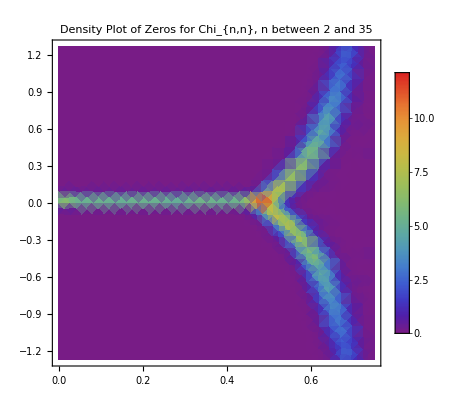

```mathematica
SmoothDensityHistogram[MapThread[List,{Re[rootsChromaticExample],Im[rootsChromaticExample]}],0.02,"PDF",ColorFunction->"Rainbow",Mesh->0,PlotLegends->Automatic,PlotLabel->"Density Plot of Zeros for Chi_{n,n}, n between 2 and 35",PlotRange->Full]
```

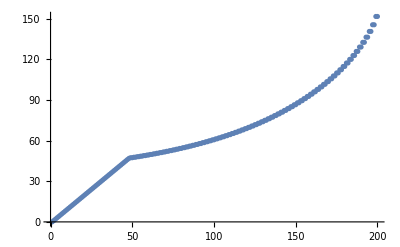

```mathematica
ListPlot[Abs[N[q/.chromaticRoots[100,100]]]]
```

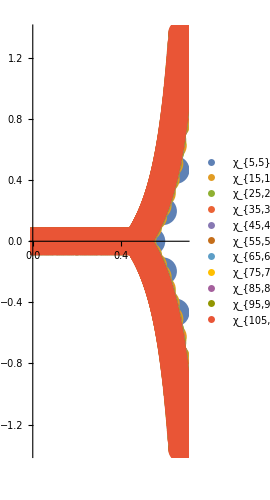

```mathematica
ComplexListPlot[Table[(q/n)/.chromaticRoots[n,n],{n,5,105,10}], PlotStyle->PointSize[0.05],PlotLegends->PointLegend[Automatic,Table[StringForm["χ_{``,``}",n,n],{n,5,105,10}]]]
```

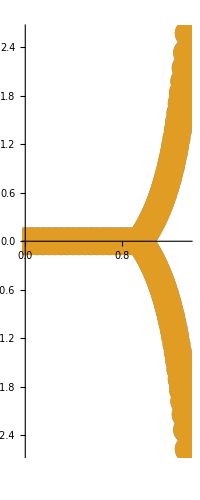

```mathematica
ComplexListPlot[{Flatten[(q/(1640/81))/.chromaticRoots[40,41]],Flatten[(q/20)/.chromaticRoots[40,40]]},PlotStyle->PointSize[0.05]]
```

## First Derivative of Chi_n,n

```mathematica
ComplexPlot3D[chromaticPolynomial[6,6]/(q-2)^2,{q,1-I,3+I},PlotLegends->Automatic]
```

-Graphics3D-

## Stirling Coefficients

```mathematica
ListPlot[Table[StirlingS2[200,i+1]/StirlingS2[200,i],{i,1,199}],PlotRange->Full]
```

-Graphics-

```mathematica
N[Flatten[Table[Position[Table[StirlingS2[n,i],{i,0,n}],Max[Table[StirlingS2[n,i],{i,0,n}]]]/n,{n,1,1000}]]]
```

{2.,1.,1.5,1.,0.75,0.8,0.666667,0.714286,0.625,0.555556,0.6,0.545455,0.5,0.538462,0.5,0.466667,0.5,0.470588,0.444444,0.473684,0.45,0.428571,0.454545,0.434783,0.416667,0.44,0.423077,0.407407,0.392857,0.413793,0.4,0.387097,0.40625,0.393939,0.382353,0.371429,0.388889,0.378378,0.368421,0.384615,0.375,0.365854,0.357143,0.372093,0.363636,0.355556,0.347826,0.361702,0.354167,0.346939,0.34,0.352941,0.346154,0.339623,0.333333,0.345455,0.339286,0.333333,0.327586,0.338983,0.333333,0.327869,0.322581,0.333333,0.328125,0.323077,0.318182,0.328358,0.323529,0.318841,0.314286,0.323944,0.319444,0.315068,0.310811,0.32,0.315789,0.311688,0.307692,0.316456,0.3125,0.308642,0.304878,0.313253,0.309524,0.305882,0.302326,0.298851,0.306818,0.303371,0.3,0.296703,0.304348,0.301075,0.297872,0.294737,0.302083,0.298969,0.295918,0.292929,0.29,0.29703,0.294118,0.291262,0.288462,0.295238,0.292453,0.28972,0.287037,0.293578,0.290909,0.288288,0.285714,0.283186,0.289474,0.286957,0.284483,0.282051,0.288136,0.285714,0.283333,0.280992,0.278689,0.284553,0.282258,0.28,0.277778,0.275591,0.28125,0.27907,0.276923,0.274809,0.280303,0.278195,0.276119,0.274074,0.272059,0.277372,0.275362,0.273381,0.271429,0.276596,0.274648,0.272727,0.270833,0.268966,0.273973,0.272109,0.27027,0.268456,0.266667,0.271523,0.269737,0.267974,0.266234,0.270968,0.269231,0.267516,0.265823,0.264151,0.26875,0.267081,0.265432,0.263804,0.262195,0.266667,0.26506,0.263473,0.261905,0.260355,0.264706,0.263158,0.261628,0.260116,0.258621,0.262857,0.261364,0.259887,0.258427,0.26257,0.261111,0.259669,0.258242,0.256831,0.26087,0.259459,0.258065,0.256684,0.255319,0.259259,0.257895,0.256545,0.255208,0.253886,0.257732,0.25641,0.255102,0.253807,0.252525,0.256281,0.255,0.253731,0.252475,0.251232,0.254902,0.253659,0.252427,0.251208,0.25,0.253589,0.252381,0.251185,0.25,0.248826,0.252336,0.251163,0.25,0.248848,0.247706,0.251142,0.25,0.248869,0.247748,0.246637,0.25,0.248889,0.247788,0.246696,0.245614,0.248908,0.247826,0.246753,0.24569,0.244635,0.247863,0.246809,0.245763,0.244726,0.243697,0.246862,0.245833,0.244813,0.243802,0.242798,0.245902,0.244898,0.243902,0.242915,0.241935,0.24498,0.244,0.243028,0.242063,0.241107,0.244094,0.243137,0.242188,0.241245,0.24031,0.243243,0.242308,0.241379,0.240458,0.239544,0.242424,0.241509,0.240602,0.2397,0.238806,0.237918,0.240741,0.239852,0.238971,0.238095,0.237226,0.24,0.23913,0.238267,0.23741,0.236559,0.239286,0.238434,0.237589,0.236749,0.235915,0.238596,0.237762,0.236934,0.236111,0.235294,0.237931,0.237113,0.236301,0.235495,0.234694,0.233898,0.236486,0.23569,0.234899,0.234114,0.233333,0.23588,0.235099,0.234323,0.233553,0.232787,0.235294,0.234528,0.233766,0.23301,0.232258,0.234727,0.233974,0.233227,0.232484,0.231746,0.231013,0.233438,0.232704,0.231975,0.23125,0.23053,0.232919,0.232198,0.231481,0.230769,0.230061,0.232416,0.231707,0.231003,0.230303,0.229607,0.228916,0.231231,0.230539,0.229851,0.229167,0.228487,0.230769,0.230088,0.229412,0.228739,0.22807,0.230321,0.229651,0.228986,0.228324,0.227666,0.227011,0.229226,0.228571,0.22792,0.227273,0.226629,0.228814,0.228169,0.227528,0.226891,0.226257,0.225627,0.227778,0.227147,0.226519,0.225895,0.225275,0.227397,0.226776,0.226158,0.225543,0.224932,0.227027,0.226415,0.225806,0.225201,0.224599,0.224,0.226064,0.225464,0.224868,0.224274,0.223684,0.225722,0.225131,0.224543,0.223958,0.223377,0.222798,0.224806,0.224227,0.22365,0.223077,0.222506,0.22449,0.223919,0.22335,0.222785,0.222222,0.221662,0.223618,0.223058,0.2225,0.221945,0.221393,0.223325,0.222772,0.222222,0.221675,0.22113,0.220588,0.222494,0.221951,0.221411,0.220874,0.220339,0.222222,0.221687,0.221154,0.220624,0.220096,0.21957,0.221429,0.220903,0.220379,0.219858,0.21934,0.221176,0.220657,0.220141,0.219626,0.219114,0.218605,0.220418,0.219907,0.2194,0.218894,0.218391,0.220183,0.21968,0.219178,0.218679,0.218182,0.217687,0.219457,0.218962,0.218468,0.217978,0.217489,0.219239,0.21875,0.218263,0.217778,0.217295,0.216814,0.218543,0.218062,0.217582,0.217105,0.21663,0.216157,0.217865,0.217391,0.21692,0.21645,0.215983,0.217672,0.217204,0.216738,0.216274,0.215812,0.215352,0.217021,0.216561,0.216102,0.215645,0.21519,0.216842,0.216387,0.215933,0.215481,0.215031,0.214583,0.216216,0.215768,0.215321,0.214876,0.214433,0.213992,0.215606,0.215164,0.214724,0.214286,0.213849,0.215447,0.21501,0.214575,0.214141,0.21371,0.21328,0.214859,0.214429,0.214,0.213573,0.213147,0.212724,0.214286,0.213861,0.213439,0.213018,0.212598,0.214145,0.213725,0.213307,0.212891,0.212476,0.212062,0.213592,0.213178,0.212766,0.212355,0.211946,0.211538,0.213052,0.212644,0.212237,0.211832,0.211429,0.211027,0.212524,0.212121,0.21172,0.211321,0.210923,0.212406,0.212008,0.21161,0.211215,0.210821,0.210428,0.211896,0.211503,0.211111,0.210721,0.210332,0.209945,0.211397,0.211009,0.210623,0.210238,0.209854,0.211293,0.210909,0.210526,0.210145,0.209765,0.209386,0.210811,0.210432,0.210054,0.209677,0.209302,0.208929,0.210339,0.209964,0.209591,0.20922,0.20885,0.208481,0.209877,0.209507,0.209139,0.208772,0.208406,0.208042,0.209424,0.209059,0.208696,0.208333,0.207972,0.209343,0.208981,0.208621,0.208262,0.207904,0.207547,0.208904,0.208547,0.208191,0.207836,0.207483,0.207131,0.208475,0.208122,0.20777,0.20742,0.207071,0.206723,0.208054,0.207705,0.207358,0.207012,0.206667,0.206323,0.207641,0.207297,0.206954,0.206612,0.206271,0.207578,0.207237,0.206897,0.206557,0.206219,0.205882,0.207178,0.20684,0.206504,0.206169,0.205835,0.205502,0.206785,0.206452,0.206119,0.205788,0.205457,0.205128,0.2064,0.20607,0.205742,0.205414,0.205087,0.204762,0.206022,0.205696,0.205371,0.205047,0.204724,0.204403,0.205651,0.205329,0.205008,0.204688,0.204368,0.205607,0.205288,0.204969,0.204651,0.204334,0.204019,0.205247,0.204931,0.204615,0.204301,0.203988,0.203675,0.204893,0.20458,0.204268,0.203957,0.203647,0.203338,0.204545,0.204236,0.203927,0.20362,0.203313,0.203008,0.204204,0.203898,0.203593,0.203288,0.202985,0.202683,0.203869,0.203566,0.203264,0.202963,0.202663,0.202363,0.20354,0.20324,0.202941,0.202643,0.202346,0.20205,0.203216,0.20292,0.202624,0.202329,0.202035,0.201742,0.202899,0.202605,0.202312,0.20202,0.201729,0.201439,0.202586,0.202296,0.202006,0.201717,0.201429,0.201141,0.202279,0.201991,0.201705,0.201418,0.201133,0.200849,0.201977,0.201693,0.201408,0.201125,0.200843,0.200561,0.201681,0.201399,0.201117,0.200837,0.200557,0.200278,0.201389,0.20111,0.200831,0.200553,0.200276,0.2,0.201102,0.200825,0.200549,0.200274,0.2,0.199726,0.20082,0.200546,0.200272,0.2,0.199728,0.200814,0.200542,0.200271,0.2,0.19973,0.199461,0.200538,0.200269,0.2,0.199732,0.199465,0.199198,0.198932,0.2,0.199734,0.199468,0.199203,0.198939,0.198675,0.199735,0.199472,0.199208,0.198946,0.198684,0.198423,0.199475,0.199214,0.198953,0.198693,0.198433,0.198175,0.199219,0.19896,0.198701,0.198444,0.198187,0.19793,0.198966,0.19871,0.198454,0.198198,0.197943,0.197689,0.198718,0.198464,0.19821,0.197957,0.197704,0.197452,0.198473,0.198221,0.19797,0.197719,0.197468,0.197219,0.198232,0.197982,0.197733,0.197484,0.197236,0.196989,0.197995,0.197747,0.1975,0.197253,0.197007,0.196762,0.197761,0.197516,0.19727,0.197026,0.196782,0.196539,0.197531,0.197287,0.197044,0.196802,0.19656,0.196319,0.197304,0.197062,0.196822,0.196581,0.196341,0.196102,0.19708,0.196841,0.196602,0.196364,0.196126,0.195889,0.19686,0.196622,0.196386,0.196149,0.195913,0.195678,0.196643,0.196407,0.196172,0.195938,0.195704,0.195471,0.196429,0.196195,0.195962,0.19573,0.195498,0.195266,0.196217,0.195986,0.195755,0.195524,0.195294,0.195065,0.194836,0.19578,0.19555,0.195322,0.195093,0.194866,0.194639,0.195576,0.195349,0.195122,0.194896,0.19467,0.194444,0.195376,0.19515,0.194925,0.1947,0.194476,0.194253,0.195178,0.194954,0.194731,0.194508,0.194286,0.194064,0.194983,0.194761,0.194539,0.194318,0.194098,0.193878,0.19479,0.19457,0.19435,0.194131,0.193912,0.193694,0.194601,0.194382,0.194164,0.193946,0.193729,0.193512,0.193296,0.194196,0.19398,0.193764,0.193548,0.193333,0.193119,0.194013,0.193798,0.193584,0.19337,0.193157,0.192944,0.193833,0.193619,0.193407,0.193194,0.192982,0.192771,0.193654,0.193443,0.193231,0.193021,0.19281,0.192601,0.193478,0.193268,0.193059,0.192849,0.192641,0.192432,0.193305,0.193096,0.192888,0.19268,0.192473,0.192266,0.19206,0.192926,0.192719,0.192513,0.192308,0.192102,0.191898,0.192758,0.192553,0.192349,0.192144,0.191941,0.191737,0.192593,0.192389,0.192186,0.191983,0.191781,0.191579,0.192429,0.192227,0.192025,0.191824,0.191623,0.191423,0.192268,0.192067,0.191867,0.191667,0.191467,0.191268,0.19107,0.191909,0.19171,0.191511,0.191313,0.191116,0.190918,0.191753,0.191555,0.191358,0.191161,0.190965,0.190769,0.191598,0.191402,0.191207,0.191011,0.190816,0.190622,0.191446,0.191251,0.191057,0.190863,0.190669,0.190476,0.191296,0.191102,0.190909,0.190716,0.190524,0.190332,0.190141,0.190955,0.190763,0.190572,0.190381,0.19019,0.19}

```mathematica
stirlingPolynomial[n_]:=Sum[StirlingS2[n,i]*q^i,{i,0,n}]
```

```mathematica
stirlingRoots[n_]:=NSolve[stirlingPolynomial[n]==0,q]
```

## Polynomial at 2

```mathematica
Table[Sum[StirlingS2[n,i]*Factorial[i-3]*(-1)^(i-3)*(i-2)^(n),{i,3,n}],{n,3,20}]
```

{1,-10,191,-6776,378477,-30305766,3283060027,-461919428212,81850834841513,-17830446084254882,4682892010746493623,-1459107131232939044208,532117038467568533681509,-224526231523742152713377758,108529290870477764007452659379,-59577291850382657673680405181164,36860036834826763092403279291112865,-25529077201590674238765830315967376794}

```mathematica
Table[2*n*(n+0.5)+2*(-1)^n*Sum[StirlingS2[n,i]*Factorial[i-3]*(i-2)^n*(-1)^{i+1},{i,3,n}],{n,3,20}]
```

{{19.},{16.},{-327.},{-13474.},{-756849.},{-6.06114×10^7},{-6.56612×10^9},{-9.23839×10^11},{-1.63702×10^14},{-3.56609×10^16},{-9.36578×10^18},{-2.91821×10^21},{-1.06423×10^24},{-4.49052×10^26},{-2.17059×10^29},{-1.19155×10^32},{-7.37201×10^34},{-5.10582×10^37}}

```mathematica
FourierTransform[chromaticPolynomial[2,2],q,omega]
```

3 ⅈ √(2 π) DiracDelta'[omega]-6 √(2 π) DiracDelta''[omega]-4 ⅈ √(2 π) DiracDelta^(3)[omega]+√(2 π) DiracDelta^(4)[omega]

```mathematica
chromaticPolynomial[2,2]
```

q (-3+6 q-4 q^2+q^3)

```mathematica
FourierTransform[Exp[1/x],x,omega]
```

$Aborted

```mathematica
LaplaceTransform[(E^x+E^y-1)^q,{x,y,q},{s1,s2,s3}]
```

$Aborted

```mathematica
FourierTransform[(2*Cos[Sin[t]]*Exp[Cos[t]]-1),t,omega]
```

$Aborted

```mathematica
FourierTransform[Exp[Cos[t]],t,omega]
```

$Aborted

```mathematica
StirlingLowerBound[m_,j_]:=((j)^(m-1)-(j-1)^m)/(Factorial[j])
```

```mathematica
Table[Table[StirlingS2[m,n] >= StirlingLowerBound[m,n],{n,0,m}],{m,0,20}]
```

Power::infy: Infinite expression 1/0 encountered.

GreaterEqual::nord: Invalid comparison with ComplexInfinity attempted.

Power::indet: Indeterminate expression 0^0 encountered.

{{1≥ComplexInfinity},{0≥Indeterminate,True},{True,True,True},{False,True,True,True},{True,True,True,True,True},{False,True,True,True,True,True},{True,True,True,True,True,True,True},{False,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True},{False,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True},{False,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True},{False,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}}

```mathematica
StirlingS2[30,5]
```

7713000216608565075

```mathematica
N[StirlingLowerBound[30,5]]
```

1.5426×10^18

```mathematica
Sum[StirlingS2[20,k]*FactorialPower[9,k],{k,0,9}]
```

12157665459056928801

```mathematica
Log[9,12157665459056928801]
```

20

```mathematica
LaplaceTransform[(E^x+E^y-1)^q,x,s]
```

Hypergeometric2F1[-q,-q+s,1-q+s,1-ⅇ^y]/(-q+s)

```mathematica
LaplaceTransform[LaplaceTransform[(E^x+E^y-1)^q,x,s],y,t]
```

LaplaceTransform[Hypergeometric2F1[1-q,-q,2-q,1-ⅇ^y],q→1,y,t]/(1-q)

```mathematica
LaplaceTransform[(E^x+E^y-1)^q,x,s]
```

Hypergeometric2F1[-q,-q+s,1-q+s,1-ⅇ^y]/(-q+s)

```mathematica
InverseLaplaceTransform[(E^x+E^y-1)^q,q, t]
```

InverseLaplaceTransform[(-1+ⅇ^x+ⅇ^y)^q,q,t]

```mathematica
f:=InverseLaplaceTransform[1/chromaticPolynomial[4,4],q,t]
```

```mathematica
f
```

```mathematica
ComplexPlot[f,{t,-1-I,1+I},PlotLegends->Automatic]
```

$Aborted

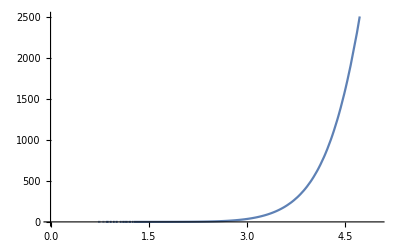

```mathematica
Plot[f,{t,0,5}]
```

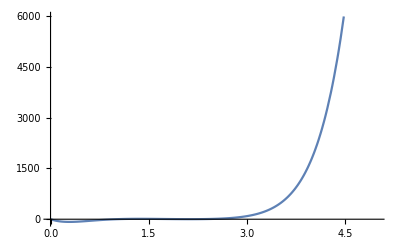

```mathematica
Plot[chromaticPolynomial[4,4],{q,0,5}]
```

## Connect Chromatic Polynomials and Euler Polynomials

```mathematica
EulerPolynomial[n_]:=Expand[Factorial[n]*Coefficient[Series[2*E^(t*x)/(1+E^t),{t,0,40}],t,n]]
```

```mathematica
EulerRoots[n_]:=NSolve[EulerPolynomial[n]==0,x,WorkingPrecision->Log[n+2]]
```

```mathematica
alternatingChromatic[k_]:=Expand[Sum[(-1)^(m)*chromaticPolynomial[m,k-m],{m,0,k}]]
```

-42433626725491925313195071185 q+69800518180683022585497158540 q^3-34445175071719347743708998422 q^5+8094291702003208488520547580 q^7-1109548013969333056432816645 q^9+99552726926288490622750320 q^11-6298371998796039494578120 q^13+296011619043033857743728 q^15-10740873448859957658450 q^17+309965414811154588200 q^19-7283895292822820100 q^21+142073449019915400 q^23-2337014611147554 q^25+32856715073840 q^27-399363698760 q^29+4238302640 q^31-39617565 q^33+329004 q^35-2470 q^37+20 q^39+q^40

```mathematica
Expand[(EulerPolynomial[40]/.x->(q+1))-(alternatingChromatic[40])]
```

0

```mathematica
Expand[EulerPolynomial[4]/.x->(q+1)]
```

-q+2 q^3+q^4

```mathematica
alternatingChromatic[4]
```

-q+2 q^3+q^4

```mathematica
alternatingChromaticNormalized[k_]:=Expand[Sum[(-1)^(m)*normalizedChromaticPolynomial[m,k-m],{m,0,k}]]
```

```mathematica
alternatingChromaticnNormalized[k_]:=Expand[Sum[(-1)^(m)*nNChromaticPolynomial[m,k-m],{m,0,k}]]
```

```mathematica
alternatingChromaticnNormalized[10]
```

(40697 q)/100800-(6117791 q^2)/2016000+(7330259 q^3)/806400-(215704373 q^4)/14400000+(112223171 q^5)/7200000-(262974107 q^6)/24000000+(638625673 q^7)/120000000-(175163021 q^8)/100000000+(72060069 q^9)/200000000-(72060069 q^10)/2000000000

```mathematica
EulerPolynomial[6]
```

-3 x+5 x^3-3 x^5+x^6

```mathematica
0.5*(Expand[(EulerPolynomial[6]/.x->(q+1))- (EulerPolynomial[6]/.x->q)])
```

0.5 (6 q-10 q^3+6 q^5)

```mathematica
Simplify[chromaticPolynomial[4,0]-chromaticPolynomial[3,1]+chromaticPolynomial[2,2]-chromaticPolynomial[1,3]+chromaticPolynomial[0,4]]
```

q (-1+2 q^2)

```mathematica
Simplify[0.5*((EulerPolynomial[4]/.x->(q+1))+(EulerPolynomial[4]/.x->(q-4)))]
```

190.-176. q+60. q^2-8. q^3+1. q^4

```mathematica
Simplify[EulerPolynomial[4]/.x->(q+1)]
```

q (-1+2 q^2+q^3)

## Alternating Chromatic Roots

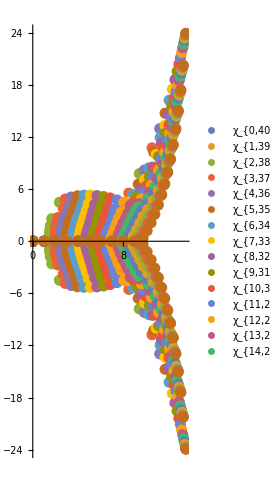

```mathematica
alternatingFourty=ComplexListPlot[Table[q/.chromaticRoots[m,40-m],{m,0,20}],PlotStyle->PointSize[0.02],PlotLegends->PointLegend[Automatic,Table[StringForm["χ_{``,``}",m,40-m],{m,0,20}]]]
```

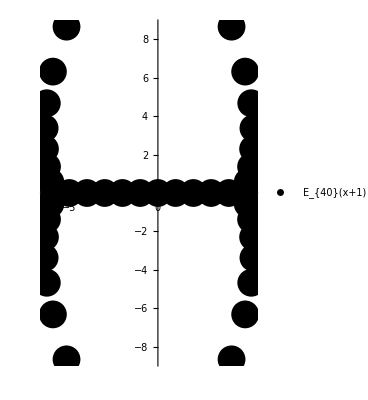

```mathematica
eulerPlot=ComplexListPlot[(x-1)/.EulerRoots[40],PlotStyle->{Black,PointSize[0.05]},PlotLegends->PointLegend[{Black},{"E_{40}(x+1)"}]]
```



```mathematica
circle=Graphics[Circle[{40/(Pi*E),0},40/(Pi*E)]]
```

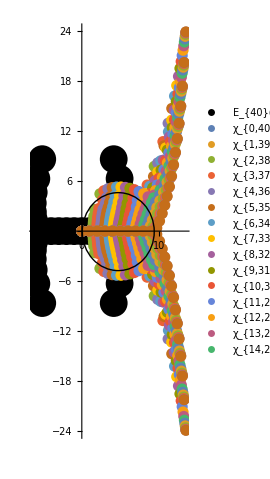

```mathematica
Show[eulerPlot,alternatingFourty,circle,PlotRange->Automatic]
```

```mathematica
A:=chromaticPolynomial[10,10]
```

```mathematica
B:=chromaticPolynomial[9,11]
```

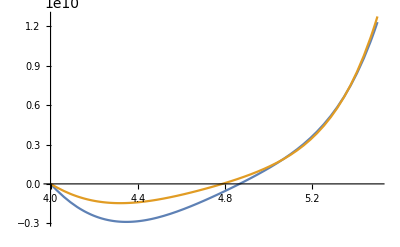

```mathematica
Plot[{A,B},{q,4,5.5}]
```